```mathematica
Get["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\Mathematica\\CDTFunctions.wl"]
```

## Analytic Comparison

```mathematica
groundTruth = VPCounts[14,3];
groundTruth=KeySortBy[groundTruth,groundTruth[#]&];
groundTruthNorm=groundTruth/Total[groundTruth];
order = Keys[groundTruth];
```

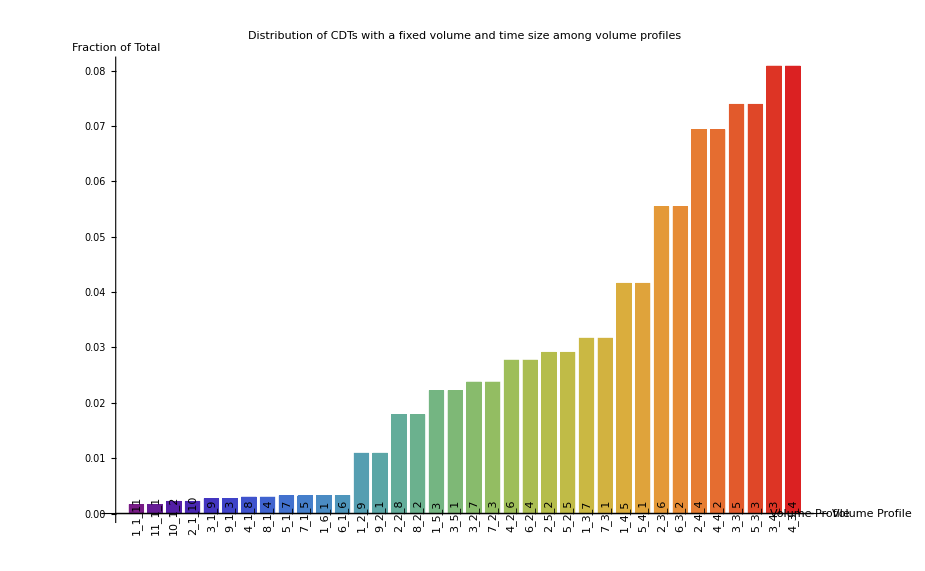

```mathematica
BarChart[groundTruthNorm,ChartLabels->Placed[Automatic,Axis,Rotate[#,Pi/2]&],ChartStyle->"Rainbow",AxesLabel->{"Volume Profile","Fraction of Total"},PlotLabel-> "Distribution of CDTs with a fixed volume and time size among volume profiles"]
```

```mathematica
folder="C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data";
files=FileNames["Statistical_Volume_14_TimeSize_3*.csv",folder];
vpData = LoadVPData[files];
```

```mathematica
vpCountsNormed =Association[Table[stepCount-> Table[SortNormCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

```mathematica
vpCounts =Association[Table[stepCount-> Table[SortCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

```mathematica
vpCountsScaled =Association[Table[stepCount-> Table[Total[groundTruth]SortNormCounts[Counts[vpData[stepCount][[index]]],order],{index,Length[vpData[stepCount]]}],{stepCount,Keys[vpData]}]];
```

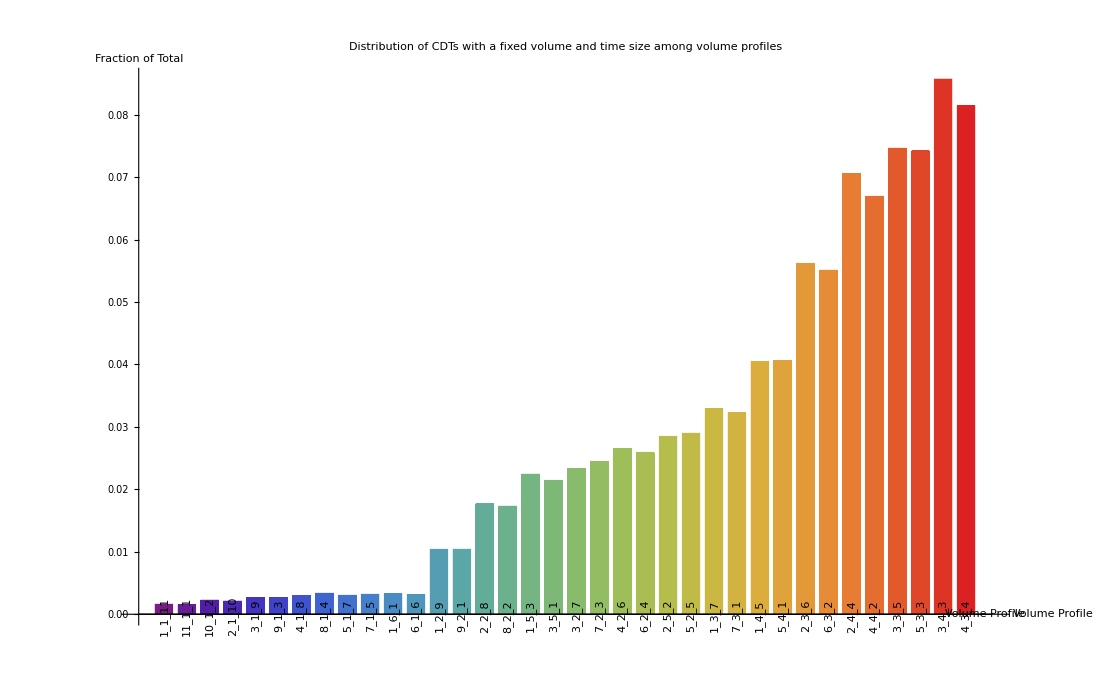

```mathematica
trialIndex = 1;
BarChart[vpCountsNormed[1][[trialIndex]][[order]],ChartLabels->Placed[Automatic,Axis,Rotate[#,Pi/2]&],ChartStyle->"Rainbow",AxesLabel->{"Volume Profile","Fraction of Total"},PlotLabel-> "Distribution of CDTs with a fixed volume and time size among volume profiles"]
```

```mathematica
residuals = Table[(vpcounts-groundTruthNorm)/groundTruthNorm,{vpcounts,vpCountsNormed[20]}];
```

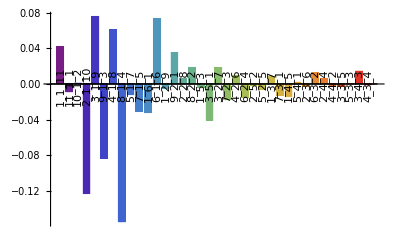

```mathematica
BarChart[residuals[[1]],ChartStyle->"Rainbow",ChartLabels->Placed[Automatic,Axis,Rotate[#,Pi/2]&]]
```

```mathematica
combinedresiduals=Merge[residuals,Join];
```

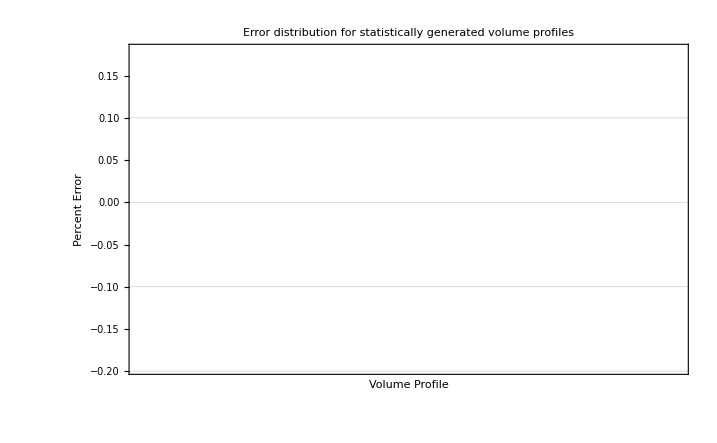

```mathematica
DistributionChart[combinedresiduals,ChartElementFunction->"Density",ChartBaseStyle->EdgeForm[],Frame->{{True,False},{False,False}},AxesLabel->{"Volume Profile","Percent Error"},PlotLabel->"Error distribution for statistically generated volume profiles",GridLines->{{}, Table[i,{i,-1,1,.1}]}]
```

## Convergance

```mathematica
files=FileNames["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Statistical_Volume_32768_TimeSize_128_*"];
data = Association[ToExpression[StringCases[#,DigitCharacter..]][[{3,4}]]->Import[#]&/@files];
```

```mathematica
getRandomMeanVP[data_]:=Module[{subdata,dataProcessed},
subdata = RandomChoice[data,1000];

dataProcessed = Table[ ToExpression@ StringSplit[vp[[1]],"_"],{vp,subdata}];
Mean[dataProcessed]


]
```

```mathematica
Keys[data]
```

{{10001,1},{1001,1},{20001,2}}

```mathematica
data[{20001,2}]
```

```mathematica
subdata =RandomChoice[data[{20001,2}],10];
dataProcessed = Table[ ToExpression@ StringSplit[vp[[1]],"_"],{vp,subdata}];
```

```mathematica
(*Calculate autocorrelation at different lags*)
ListLinePlot[Table[autoCorrelation[processeddata[[;;100,i]],lag],{i,16},{lag,0,50}]]
```

{{155_165_158_191_188_198_191_195_173_141_136_128_80_76_74_70_82_73_102_99_121_144_130_129_132_122_98_106_121_97_104_114_127_118_123_150_147_173_191_206_206_253_227_192_190_164_148_159_141_147_119_122_142_130_121_117_119_120_154_154_162_160_143_167_177_181_162_156_179_150_143_131_153_186_201_238_224_236_231_221_220_168_165_165_181_167_154_170_140_150_144_123_102_87_78_93_106_99_98_104_94_81_71_104_105_89_75_66_67_86_86_95_81_75_62_40_32_34_45_35_33_33_37_38_42_38_34_31,33748.8},{151_137_136_120_108_152_149_177_191_188_167_181_177_160_166_144_170_191_194_204_182_188_176_195_198_218_222_221_227_229_228_262_264_266_248_257_248_266_250_220_176_179_148_160_147_123_118_116_102_88_105_111_111_115_122_146_114_111_150_145_131_113_112_101_80_67_52_40_39_30_44_43_48_56_51_41_43_39_29_30_35_32_38_37_50_60_46_48_45_79_83_88_81_76_74_92_90_98_131_118_98_106_98_94_88_90_99_92_120_118_155_168_167_159_171_165_141_142_117_137_144_129_94_108_115_136_121_165,36312.3},{95_87_97_113_104_105_98_91_99_84_91_104_105_120_131_143_117_100_97_93_100_116_99_107_109_93_103_103_92_108_89_85_114_109_125_143_131_141_144_145_141_139_161_155_152_160_138_118_140_129_136_135_163_201_194_157_151_156_153_181_199_181_162_152_129_120_100_102_112_108_160_158_138_141_167_183_183_199_212_212_225_210_194_212_213_176_160_142_151_163_156_150_121_111_113_135_128_132_98_77_107_103_111_124_128_123_118_106_111_121_127_112_136_118_139_134_124_110_108_95_89_67_81_68_73_57_46_41,32573.1},{29_32_30_47_45_50_39_39_52_64_53_67_81_88_60_78_94_100_88_85_71_69_79_63_70_73_89_92_97_88_98_110_117_107_99_107_101_106_106_103_77_68_64_59_72_72_71_73_104_122_117_140_142_153_183_147_168_129_168_179_182_183_185_197_212_198_205_156_138_135_116_143_143_142_148_128_143_165_135_122_101_106_126_115_150_151_145_160_163_159_175_181_138_141_138_115_97_124_139_152_153_142_147_142_140_138_126_143_134_153_175_183_194_168_199_200_216_220_223_239_230_233_235_215_198_221_209_193,33787.2},{152_150_153_194_218_201_203_193_211_194_165_169_147_162_163_128_102_94_114_103_100_100_109_99_104_100_100_108_120_147_146_150_141_129_128_143_138_145_169_171_184_155_142_158_132_144_141_150_179_178_181_191_173_162_176_206_205_212_187_179_152_138_105_123_162_153_172_200_184_209_187_188_197_193_179_170_175_163_170_195_180_180_157_153_126_104_91_78_70_67_52_35_33_32_46_61_61_50_56_82_85_105_106_94_100_108_106_89_100_84_77_67_56_55_78_70_53_64_54_75_68_70_82_67_68_54_62_72,34591.3},{115_111_86_95_99_110_130_162_164_211_153_171_176_179_172_161_181_188_192_182_189_212_230_251_254_279_271_301_300_273_322_325_312_299_311_287_254_249_217_211_227_208_207_191_172_160_148_187_186_170_221_207_210_209_215_205_181_199_178_186_162_159_167_164_160_162_140_160_152_160_153_116_89_81_85_59_46_51_58_59_60_46_28_45_34_24_20_17_18_22_18_20_10_18_20_9_10_7_8_14_13_9_11_23_18_18_20_26_21_30_44_48_69_75_60_65_76_80_85_80_69_75_87_71_58_53_47_55,32853.6},{109_96_115_105_130_124_127_94_68_72_93_111_113_133_132_140_143_124_99_105_88_79_122_143_117_128_123_127_128_134_143_117_114_102_107_110_130_143_120_130_140_136_127_132_141_169_148_130_136_129_147_148_131_123_121_109_111_115_109_111_98_103_115_118_99_109_99_87_84_105_77_62_82_79_94_100_101_80_100_108_132_119_114_121_120_117_93_89_98_121_115_119_132_163_136_182_201_216_203_231_196_194_216_246_261_271_245_206_180_160_164_163_125_114_103_98_111_99_103_123_123_142_165_137_140_130_161_179,35496.},{127_127_136_139_130_136_121_135_121_129_135_121_112_100_102_103_113_125_118_112_86_89_111_124_121_100_92_102_90_86_78_95_72_55_64_64_67_61_61_62_51_65_71_72_88_74_70_75_45_30_35_36_43_52_42_66_59_57_62_66_49_62_65_58_65_56_53_52_62_70_76_103_126_118_119_115_103_99_101_104_105_92_95_94_86_129_143_153_160_169_173_185_185_194_210_211_211_218_221_213_222_255_249_240_238_235_239_251_274_245_252_240_237_241_248_229_216_226_210_214_220_198_187_205_219_200_185_177,35303.1},{70_78_88_99_109_98_94_106_92_102_79_77_74_70_68_63_64_65_66_95_107_91_77_54_73_84_110_117_119_117_74_72_71_68_74_75_68_62_85_86_81_104_93_87_72_86_97_100_91_96_107_102_91_83_65_67_85_92_116_116_110_144_134_148_134_133_132_118_129_133_126_122_123_137_146_146_148_136_158_176_172_160_160_164_146_192_180_226_254_225_210_208_220_222_256_281_290_277_239_218_199_194_182_178_189_183_163_172_186_147_137_124_114_118_125_126_147_153_140_145_125_127_137_145_147_157_172_164,34107.6},{158_164_161_111_111_110_108_114_136_131_119_121_101_81_68_69_72_52_53_40_36_45_49_62_74_79_88_116_125_149_165_170_164_161_141_169_168_159_170_181_184_191_184_191_186_202_198_178_199_178_146_140_128_135_129_135_155_165_172_167_156_155_128_136_107_146_147_125_137_98_101_109_101_121_98_93_88_72_51_48_54_60_79_60_74_87_81_87_74_76_87_105_97_103_102_106_94_94_83_84_89_89_89_95_109_128_118_141_115_140_155_138_139_134_139_135_142_180_241_224_232_239_237_267_293_270_239_256,37647.2}}

```mathematica
Dimensions[subdata]
```

{10,2}

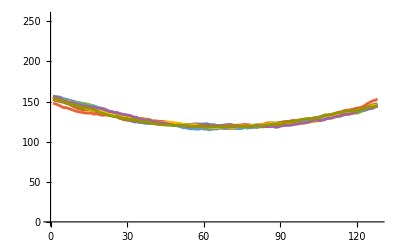

```mathematica
ListLinePlot[Table[getRandomMeanVP[data[{20001,2}]],10]//N,PlotRange->{0,256}]
```

```mathematica
Norm[{2,2,2}]
```

2 √3

```mathematica
AverageDistance[vectors_List]:=Module[{distances,totalDistance},distances=DistanceMatrix[vectors];
totalDistance=Total[Flatten[distances]]-Total[Diagonal[distances]];
totalDistance/(Length[vectors] (Length[vectors]-1))]
```

```mathematica
ListPlot[Table[AverageDistance[Table[getRandomMeanVP[data[{T,1}]],50]]//N,{T,20}]]
```

$Aborted

```mathematica
AverageDistance[Table[getRandomMeanVP[data[{10,1}]],10]]//N
```

0.281643

```mathematica
AverageDistance[Table[getRandomMeanVP[data[{20,1}]],10]]//N
```

0.307302

```mathematica
subdata = data[{20001,2}]
```

```mathematica
processeddata = Table[ ToExpression@ StringSplit[vp[[1]],"_"],{vp,subdata}];
```

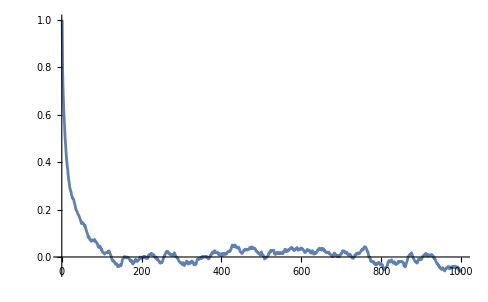

```mathematica
(*Define a function to calculate autocorrelation*)
autoCorrelation[data_,lag_]:=Module[{n,mean,denom,numer},n=Length[data];
mean=Mean[data];
denom=Sum[(data[[i]]-mean)^2,{i,lag+1,n}];
numer=Sum[(data[[i]]-mean)*(data[[i-lag]]-mean),{i,lag+1,n}];
numer/denom]
(*Calculate autocorrelation at different lags*)
ListLinePlot[ParallelTable[autoCorrelation[processeddata[[;;10000,i]],lag],{i,1},{lag,0,1000}],PlotRange->All]
```

```mathematica
Animate[ListPlot[Mean[Table[processeddata[[i+j]],{j,100}]],PlotRange-> {0,32}],{i,1,100000-100,1},AnimationRate->100]
```

0

```mathematica
Smoothness[v_]:=
Norm[Differences[v]]
```

```mathematica
distFromFlatData = Table[EuclideanDistance[d,flatVP],{d,processeddata}];
```

```mathematica
smoothnessData = Table[Smoothness[d],{d,processeddata}];
```

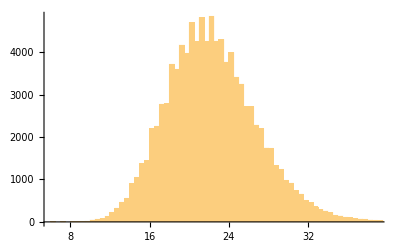

```mathematica
Histogram[smoothnessData,100]
```

```mathematica
Manipulate[Histogram[smoothnessData[[i;;i+1000]],{2.5},PlotRange->{{0,40},{0,400}}],{i,1,100000-1000,1}]
```

Part::take: Cannot take positions 99000 through 100000 in smoothnessData.

Histogram::ldata: smoothnessData⟦99000;;100000⟧ is not a valid dataset or list of datasets.

Part::take: Cannot take positions 99000 through 100000 in smoothnessData.

Histogram::ldata: smoothnessData⟦99000;;100000⟧ is not a valid dataset or list of datasets.

```mathematica
128*128*2-(2*Table[129,126]//Total)
```

260

```mathematica
flatVP = ({130}~Join~Table[129,126]~Join~{130});
```

{72,69,86,79,80,69,90,95,77,91,92,79,84,87,106,138,165,154,145,182,208,178,188,175,157,143,134,122,124,150,169,134,135,137,110,101,85,74,74,69,88,75,72,82,63,65,75,72,77,105,116,100,84,74,87,116,126,142,131,131,142,137,140,123,129,137,152,156,139,131,147,128,133,149,160,166,156,153,135,128,154,169,150,132,134,141,134,127,131,134,164,169,163,188,188,165,143,128,152,162,165,140,124,109,120,133,130,135,142,152,154,150,180,177,142,138,139,150,159,133,137,122,140,133,139,143,188,178}

```mathematica
autocorrelation=ListCorrelate[#,#,1]&/@Transpose[processeddata[[;;,;;]]];
```

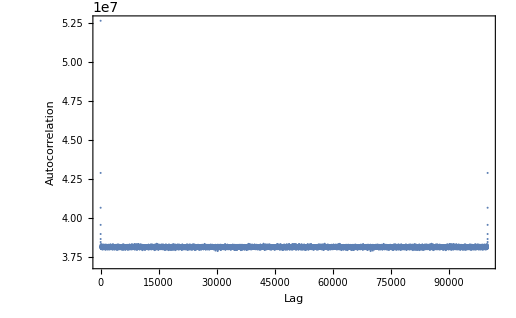

{100,127}

```mathematica
ListPlot[autocorrelation[[1]],PlotRange->All,Frame->True,FrameLabel->{"Lag","Autocorrelation"}]
```

```mathematica
(*Define the autocorrelation function*)Autocorrelation[list_]:=Module[
{n=Length[list],mean=Mean[list],var=Variance[list]},
Table[1/(n-k) Sum[(list[[i]]-mean).(list[[i+k]]-mean),{i,1,n-k}],{k,0,n-1}]]

(*Define the autocorrelation function*)Autocorrelation[list_,maxLag_]:=Module[{n=Length[list],mean=Mean[list],cov=Covariance[list]},Table[1/(n-k) Sum[(list[[i]]-mean).Inverse[cov].(list[[i+k]]-mean),{i,1,n-k}],{k,0,Min[n-1,maxLag]}]]

(*Define the autocorrelation function*)Autocorrelation[list_,maxLag_]:=Module[{n=Length[list],mean=Mean[list],var=Variance[list]},Table[If[var[[j]]!=0,1/(n-k) Sum[(list[[i,j]]-mean[[j]]) (list[[i+k,j]]-mean[[j]]),{i,1,n-k}],0],{j,1,Length[list[[1]]]},{k,0,Min[n-1,maxLag]}]/var]

(*Define the function to apply autocorrelation to each element of the vectors*)
AutocorrelationOfElements[vectors_List,maxLag_]:=Table[Autocorrelation[vectors[[All,i]],maxLag],{i,1,Length[vectors[[1]]]}]



Variance[processeddata[[;;10]]]
```

{1357/18,5461/90,2428/45,2909/90,1106/15,1987/30,138/5,1027/30,3389/90,823/30,1781/90,76/3,1622/45,6421/90,1316/15,18121/90}

```mathematica
autocorrelation=AutocorrelationOfElements[processeddata[[;;100]]//N,10]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
ListPlot[autocorrelation]
```

-Graphics-

```mathematica
Dimensions[autocorrelation]
```

{100000,16}

```mathematica
Dimensions[processeddata[[;;10]]]
```

{10,16}

{23,8,43,45,26,14,6,7,12,23,30,6,30,37,2,9,7,21,20,3,4,32,12,25,6,6,10,21,32,23,20,3,11,2,10,11,48,28,34,28,22,23,17,24,13,12,23,36,23,35,49,50,14,31,25,14,9,13,5,22,10,6,33,52,43,19,20,27,34,23,40,19,23,23,43,31,29,11,6,10,17,25,9,14,14,5,26,12,12,26,7,18,15,10,34,44,20,21,60,36,5,11,33,21,40,24,23,15,40,7,16,35,30,24,9,21,18,4,17,2,22,38,26,32,12,22,28,18,17,6,20,5,34,17,19,48,41,24,22,35,12,20,41,17,16,27,19,25,42,7,9,21,29,11,8,15,22,16,35,30,14,14,15,19,26,22,59,55,49,53,33,9,2,15,13,8,12,17,5,28,16,34,27,14,38,22,35,23,20,14,27,20,9,6,10,14,15,39,13,9,18,42,12,27,17,6,19,19,12,18,5,7,11,3,10,21,6,7,9,7,23,5,14,9,16,16,3,18,17,18,36,22,27,15,74,8,30,24,21,9,31,36,16,9,35,24,15,11,29,13,8,32,28,29,29,5,6,4,14,5,14,28,27,16,8,3,9,8,15,8,12,35,16,24,19,14,4,14,4,12,41,23,23,4,12,9,19,37,17,32,20,58,33,11,21,27,6,1,35,37,16,10,12,13,7,14,43,48,37,36,28,37,8,8,9,14,8,4,15,13,5,26,24,21,2,21,14,15,21,20,19,24,53,17,10,15,2,23,31,30,44,26,11,35,30,4,33,20,16,38,15,27,23,21,10,8,6,9,22,17,23,11,2,19,12,2,20,14,21,23,38,32,23,33,29,15,8,52,21,6,3,10,4,2,28,14,11,26,28,7,38,22,13,15,43,19,8,14,28,28,39,28,12,2,13,26,23,34,16,15,24,28,13,25,27,29,42,18,16,18,36,44,27,16,11,14,12,5,3,20,22,6,23,19,55,28,9,12,30,17,12,2,1,24,23,33,33,16,12,10,4,11,9,5,16,7,12,7,12,8,15,27,15,31,8,20,44,36,36,19,25,22,31,22,24,10,13,8,7,12,10,10,16,15,25,19,10,30,24,11,23,6,13,19,17,4,45,17,10,11,2,20,19,40,16,9,14,1,6,32,22,45,27,8,9,8,6,15,12,27,15,26,41,36,44,47,36,32,36,20,25,40,18,12,27,56,27,2,7,6,6,1,1,3,7,13,5,19,4,16,20,7,21,11,14,28,42,29,19,10,18,19,18,3,14,24,6,27,27,17,22,31,9,11,12,20,11,12,14,12,28,15,15,20,37,17,21,27,40,35,37,26,24,17,20,31,41,59,38,34,34,17,28,10,16,8,11,14,12,16,18,16,12,31,28,4,25,37,24,22,28,30,47,20,32,22,33,16,13,14,10,15,19,20,15,17,29,17,11,24,29,27,19,32,27,26,21,20,18,17,40,10,9,17,31,22,21,38,6,22,16,17,5,3,19,5,10,17,15,37,24,21,12,15,11,3,4,19,13,17,9,6,28,8,11,8,4,3,34,11,7,13,3,4,18,30,38,26,18,43,50,27,52,42,6,12,14,15,2,18,15,14,21,27,23,4,9,6,10,8,8,14,7,29,13,24,24,9,4,3,12,5,9,8,8,20,14,13,35,30,12,27,45,2,5,14,4,14,9,14,26,25,16,19,16,11,33,40,26,16,12,11,4,18,17,33,1,20,1,5,17,18,21,28,25,23,50,41,10,22,17,34,28,10,9,16,13,5,3,14,4,2,9,15,17,15,26,8,3,18,9,17,23,21,17,11,15,11,17,20,13,17,3,7,2,17,6,9,14,15,26,9,23,15,6,23,15,16,8,11,9,4,8,27,10,20,33,17,10,25,30,22,6,9,45,19,11,9,14,11,5,26,24,9,13,14,21,59,38,18,36,60,6,3,26,49,10,27,4,8,12,2,13,24,29,32,2,14,16,5,16,23,26,22,22,36,40,19,6,11,7,27,25,42,30,27,21,29,28,21,9,5,35,27,62,56,25,24,32,33,29,28,28,11,20,10,22,11,39,4,7,11,10,33,5,21,20,13,21,23,22,19,12,26,47,34,29,13,25,29,9,9,28,10,4,21,20,26,47,30,2,16,13,20,10,20,12,9,4,10,8,20,9,20,20,29,11,29,20,14,15,4,23,26,23,29,17,19,37,28,20,6,2,10,14,19,30,31,22,24,7,5,17,10,25,15,18,22,8,44}

```mathematica
AutocorrelationTest[#,99]&/@Transpose[processeddata[[;;1000]]]
```

{7.91307×10^-21,2.724×10^-46,1.02401×10^-37,3.19804×10^-16,3.70082×10^-9,2.47036×10^-9,0.00914926,0.348194,0.121942,0.032593,6.87097×10^-11,1.94507×10^-18,3.91697×10^-26,3.44862×10^-34,3.27963×10^-39,1.41331×10^-13}

```mathematica
ListCorrelate[{1,2,1},{1,3,1},1]
```

{8,6,6}

```mathematica
(*Let's assume you have a time series data*)timeSeries=RandomReal[1,100];

(*Define a function to calculate autocorrelation*)
autoCorrelation[data_,lag_]:=Module[{n,mean,denom,numer},n=Length[data];
mean=Mean[data];
denom=Sum[(data[[i]]-mean)^2,{i,lag+1,n}];
numer=Sum[(data[[i]]-mean)*(data[[i-lag]]-mean),{i,lag+1,n}];
numer/denom]

(*Calculate autocorrelation at different lags*)
ListLinePlot[Table[autoCorrelation[processeddata[[;;100,i]],lag],{i,16},{lag,0,50}]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-